```mathematica
file[n_,r_]:=StringJoin["D:\\DropBox\\coding\\step\\",ToString[n],".",ToString[r]];
list[n_,r_]:=Import[file[n,r],"Table"]
(*log[n_,r_]:=Table[{Log[list[n,r][[i,1]]],Log[list[n,r][[i,2]]]},{i,Length[list[n,r]]}]*)
MatrixForm[Table[list[n,r],{n,{2,3,5,7}},{r,{2,3,5,7}}]];
prime=Import["D:\\DropBox\\coding\\step\\prime","Table"];
```

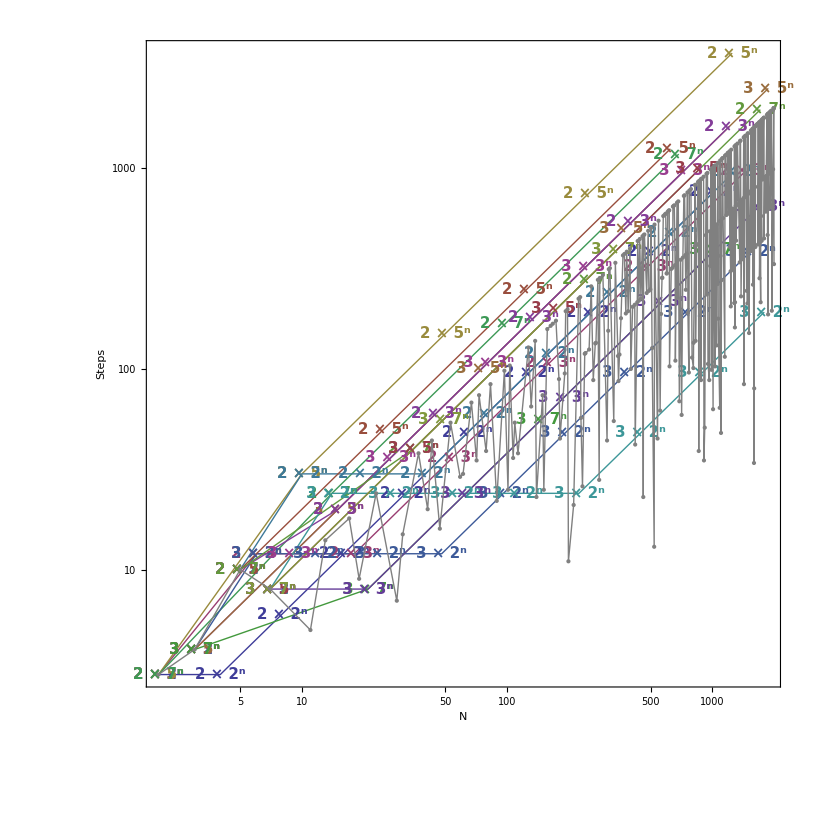

```mathematica
(*PlotMarkers->Flatten[Table[Subsuperscript[ ToString[r],ToString[n],"N"],{n,{2,3}},{r,{2,3,5,7}}],1]ListLinePlot[Flatten[Table[log[n,r],{n,{2,3}},{r,{2,3,5,7}}],1],PlotRange->All,AxesOrigin->{0,0},Mesh->All,PlotMarkers->Flatten[Table[n"×" Superscript[ ToString[r],"N"],{n,{2,3}},{r,{2,3,5,7}}],1],AxesLabel->{"Log[N]","Log[Steps]"}]*)
periodical=ListLogLogPlot[Flatten[Table[list[n,r],{n,{2,3,5,7}},{r,{2,3,5,7}}],1],PlotMarkers->Flatten[Table[Style[ToString[n]"×" Superscript[ ToString[r],"n"],Bold,15],{n,{2,3}},{r,{2,3,5,7}}],1],AxesOrigin->{0,0},PlotRange->All,Mesh->All,Joined->True,Frame->True,FrameLabel->{"N","Steps"},LabelStyle->Large,PlotStyle->Thick];
primes=ListLogLogPlot[prime,AxesOrigin->{0,0},PlotRange->All,Mesh->All,Joined->True,PlotStyle->Gray,Frame->True,FrameLabel->{"N","Steps"},LabelStyle->Large];
Show[{periodical,primes},AspectRatio->1]
```

```mathematica
label[n_,r_]:=Table[n If[i==1,1,If[i<3||(r==2&&i<6||r==3&&i<4), r^(i-1),"·"Superscript[ ToString[r],ToString[i-1]]]],{i,Length[list[n,r]]}];
label[n_,r_]:=Table[Subscript[n,Superscript[Style[ToString[r],Medium],Style[ToString[i-1],Medium]]],{i,Length[list[n,r]]}];
MatrixForm[group=Flatten[Table[{label[n,r],list[n,r]},{n,{2,3,5,7}},{r,{2,3,5,7}}],1]];
names=Join@@Table[group[[i]][[1]],{i,16}];
coords=Join@@Table[group[[i]][[2]],{i,16}];
labels=Thread[{names,coords}];
```

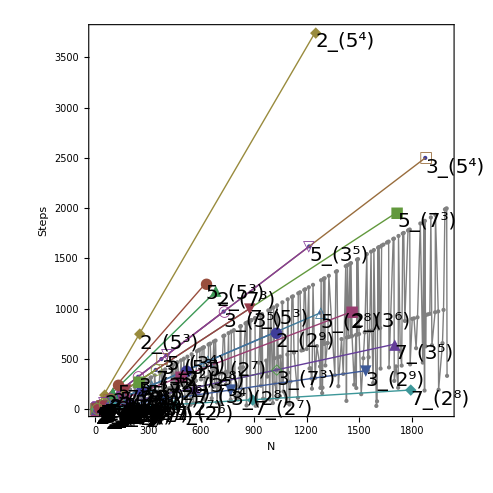

```mathematica
points=ListPlot[Table[labels[[i]][[2]],{i,Length[labels]}],Epilog->(Text[StyleForm[#[[1]],20],#[[2]]
,{-1,1}]&/@labels)];
periodical=ListPlot[Flatten[Table[list[n,r],{n,{2,3,5,7}},{r,{2,3,5,7}}],1],PlotRange->All,Joined->True,PlotStyle->Thick,PlotMarkers->{Automatic,15},Mesh->All];
primes=ListPlot[prime,PlotRange->All,Joined->True,PlotStyle->Gray,Mesh->All];
Show[{points,primes,periodical},AspectRatio->1,Frame->True,FrameLabel->{"N","Steps","Period of N×N Map"},LabelStyle->Large]
```

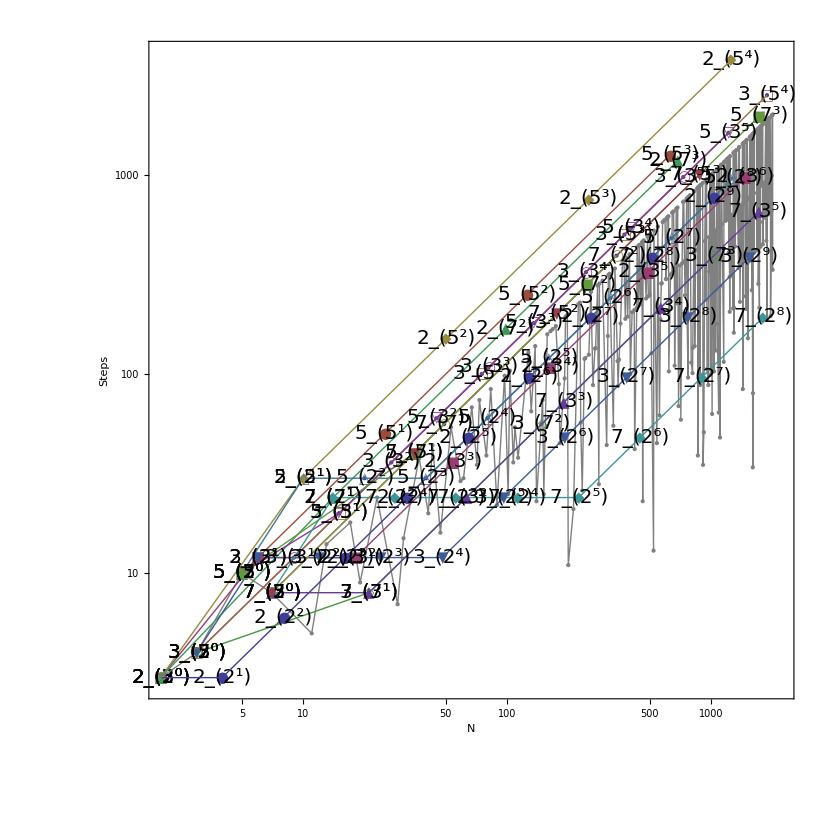

```mathematica
points=ListLogLogPlot[Table[labels[[i]][[2]],{i,Length[labels]}],Epilog->(Text[StyleForm[#[[1]],20],Log[#[[2]]],{0,0}]&/@labels),PlotRange->All];
periodical=ListLogLogPlot[Flatten[Table[list[n,r],{n,{2,3,5,7}},{r,{2,3,5,7}}],1],PlotRange->All,Joined->True,PlotStyle->Thick,PlotMarkers->{Automatic,15},Mesh->All];
primes=ListLogLogPlot[prime,PlotRange->All,Joined->True,PlotStyle->Gray,Mesh->All];
Show[{points,primes,periodical},AspectRatio->1,Frame->True,FrameLabel->{"N","Steps","Period of N×N Map"},LabelStyle->Large,PlotRange->{{0.7,7.7},{1,8.3}}]
```

```mathematica
Fit[{{2038.68,1971.54},{1413.63,1377.97},{788.44,768.923},{435.42,429.073},{222.159,220.607},{73.3378,74.5548},{37.0503,38.3327},{12.9794,14.0605}},{1,x},x]
```

4.63132+0.967404 x

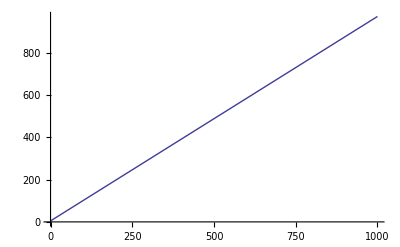

```mathematica
a=Plot[4.631315481024416+0.9674042380203189 x,{x,0,1000}]
```